## Set parameter values and define functions:

```mathematica
(*Seasonal forcing*)
beta[t_,amplitude_,baseline_,phival_,gammaval_]:=gammaval*(amplitude/2*Cos[2*Pi*(t-phival)/52]+(amplitude/2+baseline))

pC = (0.3)*(0.044); (*Probability of needing critical care*)
pH = (0.7)*(0.044); (*Probability of hospitalization but not critical care*)
pS = 1-(pC + pH); (*Probability of not needing care*)

nuval = 1/(4.6/7); (*Rate of progressing to infectiousness*)
gammaval = 1/(5/7); (*Rate of losing infectiousness or going to the hospital*)

deltaHval = 1/(8/7); (*Rate of leaving hospital for those not going to critical care*)
deltaCval = 1/(6/7); (*Rate of leaving hospital and going to critical care*)
xiCval = 1/(10/7); (*Rate of leaving critical care*)
 
amplitude = 0.6; (*0.6*)
baseline = 1.4; (*1.4*)
phival= -3.8;

kappaval = 0.01;
importtime = (31+29+11)/7; 
importlength = 0.5;

ptest = 0.05; (*probability that a non-hospitalized case gets tested*)

tmax = 5*52;

plotwindow = {0, 64};
plotwindowlong = {0, 52*2.5};
fs = 18;
imsz=400;
seasonality = 1;
```

```mathematica
thresholdprevon = 0.0035; 
thresholdprevoff = 0.001;

thresholdprevonmoreICU = 0.007; 
thresholdprevoffmoreICU = 0.002;
```

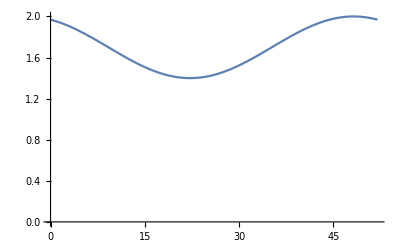

```mathematica
Plot[beta[t, amplitude, baseline, phival, 1],{t,0,52}, PlotRange->{0,2}]
```

## No-intervention simulation, with seasonality:

```mathematica
sols=NDSolve[{
Sq'[t] == -beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t]-est[t]*Sq[t] ,
Eq'[t] == beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t]+est[t]*Sq[t]  - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0, est[0]==0
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est},{t, 0, tmax}
];
```

## No-intervention simulation, no seasonality:

```mathematica
seasonality=0;
solns=NDSolve[{
Sq'[t] == -beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0, est[0]==0
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est},{t, 0, tmax}
];
```

## Scenarios with seasonality:

### 20% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 4;
seasonality=1;
sol20x2x4s=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 40% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 4;
seasonality=1;
sol40x2x4s=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 60% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 4;
seasonality=1;
sol60x2x4s=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 20% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 8;
seasonality=1;
sol20x2x8s=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 40% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 8;
seasonality=1;
sol40x2x8s=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 60% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 8;
seasonality=1;
sol60x2x8s=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 20% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 12;
seasonality=1;
sol20x2x12s=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 40% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 12;
seasonality=1;
sol40x2x12s=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 60% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 12;
seasonality=1;
sol60x2x12s=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 20% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 20;
seasonality=1;
sol20x2x20s=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 40% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 20;
seasonality=1;
sol40x2x20s=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 60% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 20;
seasonality=1;
sol60x2x20s=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 20% reduction in transmission, 2 weeks after establishment, always on, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + Infinity;
seasonality=1;
sol20x2xinfs=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 40% reduction in transmission, 2 weeks after establishment, always on, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + Infinity;
seasonality=1;
sol40x2xinfs=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 60% reduction in transmission, 2 weeks after establishment, always on, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + Infinity;
seasonality=1;
sol60x2xinfs=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

## Scenarios without seasonality:

### 20% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 4;
seasonality=0;
sol20x2x4ns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 40% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 4;
seasonality=0;
sol40x2x4ns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 60% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 4;
seasonality=0;
sol60x2x4ns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 20% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 8;
seasonality=0;
sol20x2x8ns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 40% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 8;
seasonality=0;
sol40x2x8ns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 60% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 8;
seasonality=0;
sol60x2x8ns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 20% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 12;
seasonality=0;
sol20x2x12ns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 40% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 12;
seasonality=0;
sol40x2x12ns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 60% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 12;
seasonality=0;
sol60x2x12ns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 20% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 20;
seasonality=0;
sol20x2x20ns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 40% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 20;
seasonality=0;
sol40x2x20ns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 60% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 20;
seasonality=0;
sol60x2x20ns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 20% reduction in transmission, 2 weeks after establishment, always on, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + Infinity;
seasonality=0;
sol20x2xinfns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 40% reduction in transmission, 2 weeks after establishment, always on, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + Infinity;
seasonality=0;
sol40x2xinfns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 60% reduction in transmission, 2 weeks after establishment, always on, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + Infinity;
seasonality=0;
sol60x2xinfns=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

## Scenarios without seasonality, with brake-pumping

### 20% reduction in transmission:

```mathematica
npifactor = 0.2;
seasonality=0;
sol20bpnsprev=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevon, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoff, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 40% reduction in transmission:

```mathematica
npifactor = 0.4;
seasonality=0;
sol40bpnsprev=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevon, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoff, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 60% reduction in transmission:

```mathematica
npifactor = 0.6;
seasonality=0;
sol60bpnsprev=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevon, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoff, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

## Scenarios with seasonality, with brake-pumping

### 20% reduction in transmission:

```mathematica
npifactor = 0.2;
seasonality=1;
sol20bpsprev=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevon, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoff, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 40% reduction in transmission:

```mathematica
npifactor = 0.4;
seasonality=1;
sol40bpsprev=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevon, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoff, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

### 60% reduction in transmission:

```mathematica
npifactor = 0.6;
seasonality=1;
sol60bpsprev=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevon, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoff, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

## Scenarios with seasonality, with brake-pumping, and a higher threshold assuming more ICU beds:

### 20% reduction in transmission:

```mathematica
npifactor = 0.2;
seasonality=1;
sol20bpsprevmoreICU=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevonmoreICU, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoffmoreICU, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est,npi},{t, 0, tmax}
];
```

### 40% reduction in transmission:

```mathematica
npifactor = 0.4;
seasonality=1;
sol40bpsprevmoreICU=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevonmoreICU, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoffmoreICU, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est,npi},{t, 0, tmax}
];
```

### 60% reduction in transmission:

```mathematica
npifactor = 0.6;
seasonality=1;
sol60bpsprevmoreICU=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevonmoreICU, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoffmoreICU, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est,npi},{t, 0, tmax}
];
```

## Scenarios with no seasonality, with brake-pumping, and a higher threshold assuming more ICU beds:

### 20% reduction in transmission:

```mathematica
npifactor = 0.2;
seasonality=0;
sol20bpnsprevmoreICU=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevonmoreICU, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoffmoreICU, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est,npi},{t, 0, tmax}
];
```

### 40% reduction in transmission:

```mathematica
npifactor = 0.4;
seasonality=0;
sol40bpnsprevmoreICU=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevonmoreICU, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoffmoreICU, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est,npi},{t, 0, tmax}
];
```

### 60% reduction in transmission:

```mathematica
npifactor = 0.6;
seasonality=0;
sol60bpnsprevmoreICU=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevonmoreICU, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoffmoreICU, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est,npi},{t, 0, tmax}
];
```

## Define key variables for the brake-pump strategies:

```mathematica
dateticks = {
{0, Rotate["Jan",π/2]},
{0, Text[Style["\n\n2020", FontSize->14]]},
{(31)/7,""},
{(31+28)/7,""},
{(31+28+31)/7, Rotate["Apr",π/2]}, 
{(31+28+31+30)/7,""}, 
{(31+28+31+30+31)/7,""}, 
{(31+28+31+30+31+30)/7, Rotate["July",π/2]}, 
{(31+28+31+30+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31)/7, ""},
{(31+28+31+30+31+30+31+31+30)/7, Rotate["Oct",π/2]},
{(31+28+31+30+31+30+31+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31+30+31+30)/7, ""},
{52, Rotate["Jan",π/2]},
{52, Text[Style["\n\n2021", FontSize->14]]},
{52+(31)/7,""}, 
{52+(31+28)/7, ""}, 
{52+(31+28+31)/7, Rotate["Apr",π/2]}, 
{52+(31+28+31+30)/7, ""}, 
{52+(31+28+31+30+31)/7, ""}, 
{52+(31+28+31+30+31+30)/7, Rotate["July",π/2]}, 
{52+(31+28+31+30+31+30+31)/7, ""},
{52+(31+28+31+30+31+30+31+31)/7, ""},
{52+(31+28+31+30+31+30+31+31+30)/7, Rotate["Oct",π/2]},
{52+(31+28+31+30+31+30+31+31+30+31)/7,""},
{52+(31+28+31+30+31+30+31+31+30+31+30)/7,""},
{52*2, Rotate["Jan",π/2]}, 
{52*2, Text[Style["\n\n2022", FontSize->14]]}, 
{52*2+(31)/7, ""}, 
{52*2+(31+28)/7, ""}, 
{52*2+(31+28+31)/7, Rotate["Apr",π/2]}, 
{52*2+(31+28+31+30)/7,""}, 
{52*2+(31+28+31+30+31)/7,""}, 
{52*2+(31+28+31+30+31+30)/7, Rotate["July",π/2]}, 
{52*2+(31+28+31+30+31+30+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31+30)/7, Rotate["Oct",π/2]}};
```

```mathematica
yearticks = {
{0, Rotate["2020",π/2]},
{(31)/7,""},
{(31+28)/7,""},
{(31+28+31)/7, ""}, 
{(31+28+31+30)/7,""}, 
{(31+28+31+30+31)/7,""}, 
{(31+28+31+30+31+30)/7,""}, 
{(31+28+31+30+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31)/7, ""},
{(31+28+31+30+31+30+31+31+30)/7, ""},
{(31+28+31+30+31+30+31+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31+30+31+30)/7, ""},
{52, Rotate["2021",π/2]},
{52+(31)/7,""}, 
{52+(31+28)/7, ""}, 
{52+(31+28+31)/7,""}, 
{52+(31+28+31+30)/7, ""}, 
{52+(31+28+31+30+31)/7, ""}, 
{52+(31+28+31+30+31+30)/7,""}, 
{52+(31+28+31+30+31+30+31)/7, ""},
{52+(31+28+31+30+31+30+31+31)/7, ""},
{52+(31+28+31+30+31+30+31+31+30)/7, ""},
{52+(31+28+31+30+31+30+31+31+30+31)/7,""},
{52+(31+28+31+30+31+30+31+31+30+31+30)/7,""},
{52*2, Rotate["2022",π/2]}, 
{52*2+(31)/7, ""}, 
{52*2+(31+28)/7, ""}, 
{52*2+(31+28+31)/7,""}, 
{52*2+(31+28+31+30)/7,""}, 
{52*2+(31+28+31+30+31)/7,""}, 
{52*2+(31+28+31+30+31+30)/7, ""}, 
{52*2+(31+28+31+30+31+30+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31+30)/7, ""}};
```

```mathematica
ar = 0.25;
```

```mathematica
imsz=700;
```

## Plot incidence with seasonality for fixed-duration interventions and critical care:

```mathematica
line1char = {Black};
line2char = {Red};
line3char = {Blue};
line4char = {Green};

line5char = {Black, Dashed};
line6char = {Red, Dashed};
line7char = {Blue, Dashed};
line8char = {Green, Dashed};

prmax = 800; (*800*)
```

### Four weeks:

```mathematica
sf = 40;
```

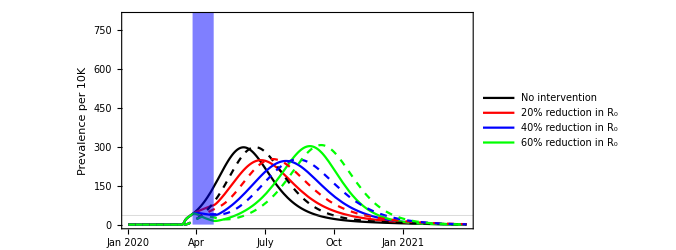

```mathematica
figoneshot4scrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x4s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x4s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x4s], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2x4s],
sf * 10000*Evaluate[CCq[t]/.sol40x2x4s],
sf * 10000*Evaluate[CCq[t]/.sol60x2x4s]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+4,1000}]}]
```

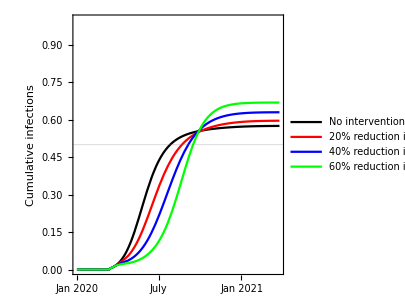

```mathematica
figoneshot4scritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2x4s],
Evaluate[1-Sq[t]/.sol40x2x4s],
Evaluate[1-Sq[t]/.sol60x2x4s],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

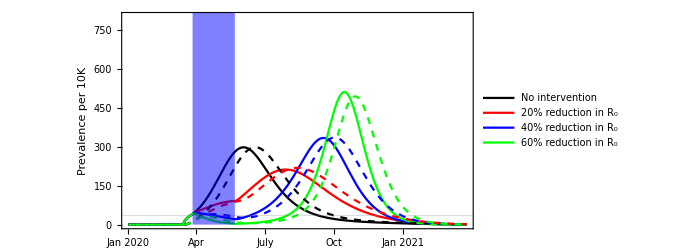

```mathematica
figoneshot8scrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x8s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x8s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x8s], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2x8s],
sf * 10000*Evaluate[CCq[t]/.sol40x2x8s],
sf * 10000*Evaluate[CCq[t]/.sol60x2x8s]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+8,1000}]}]
```

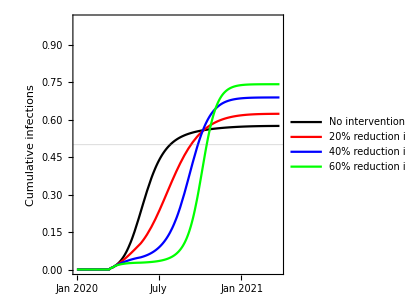

```mathematica
figoneshot8scritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2x8s],
Evaluate[1-Sq[t]/.sol40x2x8s],
Evaluate[1-Sq[t]/.sol60x2x8s],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

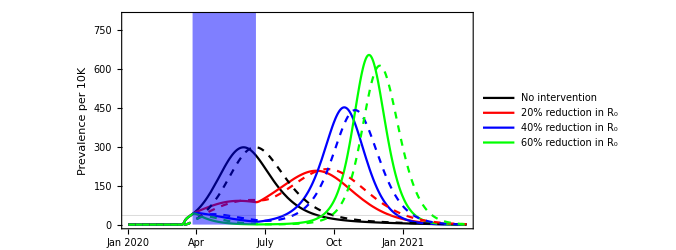

```mathematica
figoneshot12scrit =Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x12s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x12s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x12s], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2x12s],
sf * 10000*Evaluate[CCq[t]/.sol40x2x12s],
sf * 10000*Evaluate[CCq[t]/.sol60x2x12s]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+12,1000}]}]
```

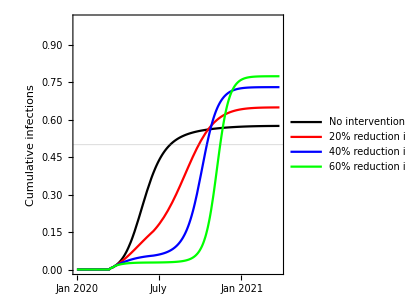

```mathematica
figoneshot12scritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2x12s],
Evaluate[1-Sq[t]/.sol40x2x12s],
Evaluate[1-Sq[t]/.sol60x2x12s],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

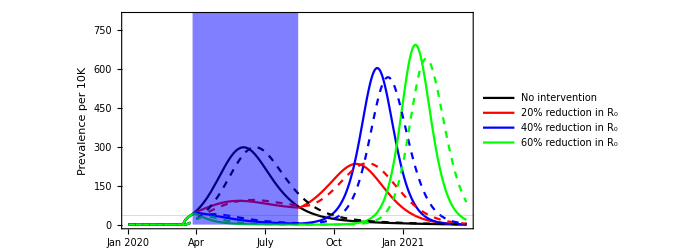

```mathematica
figoneshot20scrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x20s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x20s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x20s], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2x20s],
sf * 10000*Evaluate[CCq[t]/.sol40x2x20s],
sf * 10000*Evaluate[CCq[t]/.sol60x2x20s]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+20,1000}]}]
```

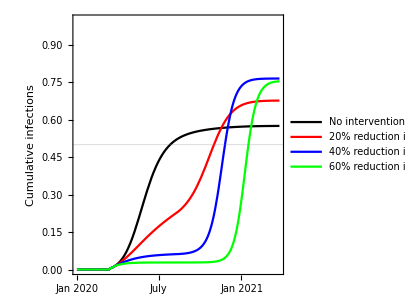

```mathematica
figoneshot20scritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2x20s],
Evaluate[1-Sq[t]/.sol40x2x20s],
Evaluate[1-Sq[t]/.sol60x2x20s],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

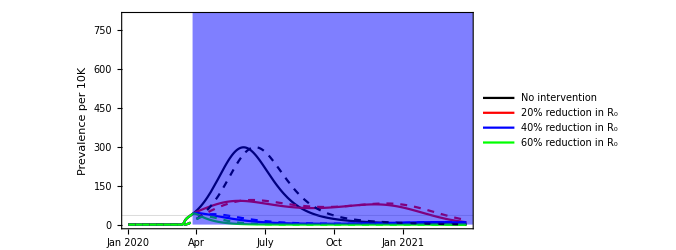

```mathematica
figoneshotinfscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2xinfs],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2xinfs],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2xinfs], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2xinfs],
sf * 10000*Evaluate[CCq[t]/.sol40x2xinfs],
sf * 10000*Evaluate[CCq[t]/.sol60x2xinfs]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+10000,1000}]}]
```

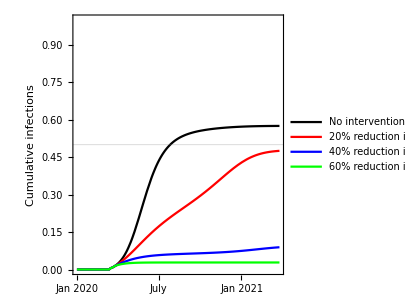

```mathematica
figoneshotinfscritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2xinfs],
Evaluate[1-Sq[t]/.sol40x2xinfs],
Evaluate[1-Sq[t]/.sol60x2xinfs],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

## Plot incidence w/out seasonality for fixed-duration interventions and critical care:

```mathematica
line1char = {Black};
line2char = {Red};
line3char = {Blue};
line4char = {Green};

line5char = {Black, Dashed};
line6char = {Red, Dashed};
line7char = {Blue, Dashed};
line8char = {Green, Dashed};

prmax = 850;
```

### Four weeks:

```mathematica
sf = 40;
```

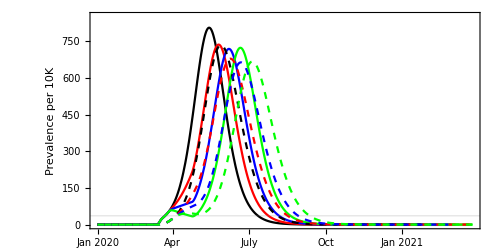

```mathematica
figoneshot4nscrittemp = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x4ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x4ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x4ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x4ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x4ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x4ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},AspectRatio->.5]
```

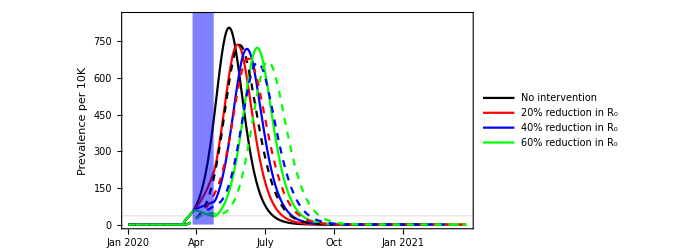

```mathematica
figoneshot4nscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x4ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x4ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x4ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x4ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x4ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x4ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[N[1/sf*#]]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+4,2000}]}]
```

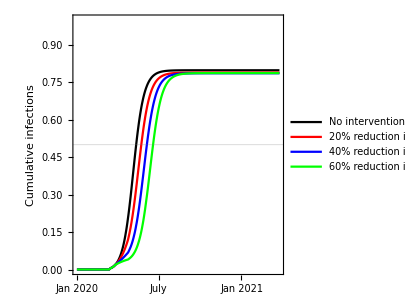

```mathematica
figoneshot4nscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2x4ns],
Evaluate[1-Sq[t]/.sol40x2x4ns],
Evaluate[1-Sq[t]/.sol60x2x4ns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

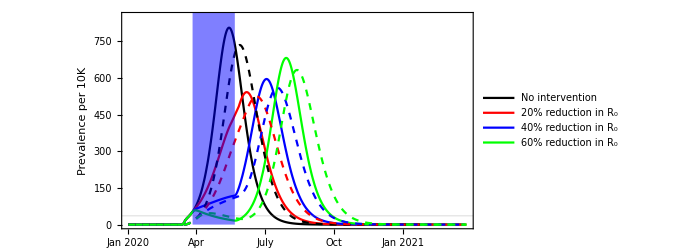

```mathematica
figoneshot8nscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x8ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x8ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x8ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x8ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x8ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x8ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+8,2000}]}]
```

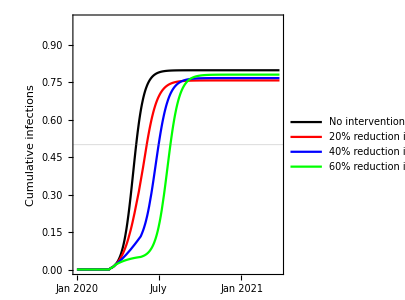

```mathematica
figoneshot8nscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2x8ns],
Evaluate[1-Sq[t]/.sol40x2x8ns],
Evaluate[1-Sq[t]/.sol60x2x8ns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

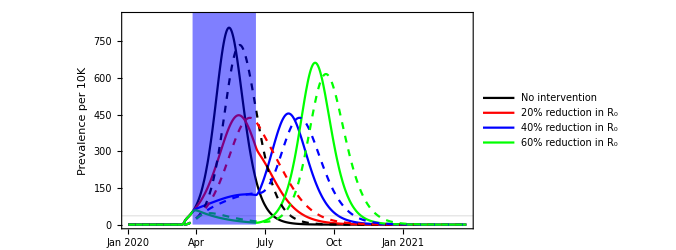

```mathematica
figoneshot12nscrit =Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x12ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x12ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x12ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x12ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x12ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x12ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+12,2000}]}]
```

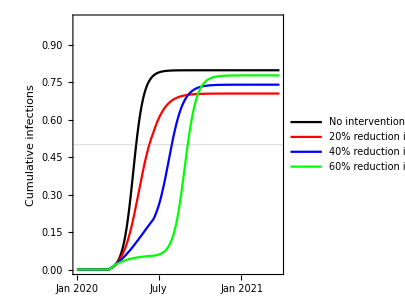

```mathematica
figoneshot12nscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2x12ns],
Evaluate[1-Sq[t]/.sol40x2x12ns],
Evaluate[1-Sq[t]/.sol60x2x12ns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

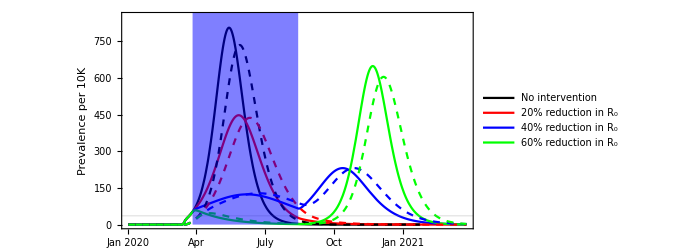

```mathematica
figoneshot20nscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x20ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x20ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x20ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x20ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x20ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x20ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+20,2000}]}]
```

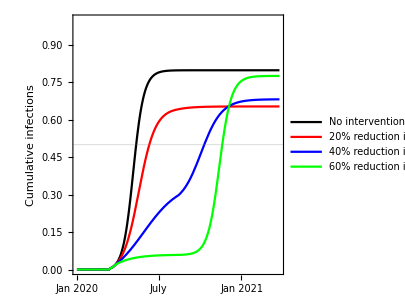

```mathematica
figoneshot20nscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2x20ns],
Evaluate[1-Sq[t]/.sol40x2x20ns],
Evaluate[1-Sq[t]/.sol60x2x20ns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

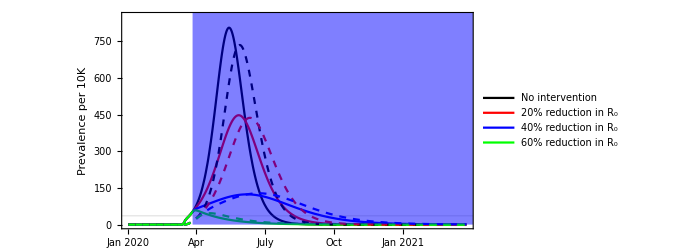

```mathematica
figoneshotinfnscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2xinfns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2xinfns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2xinfns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2xinfns],
sf * 10000*Evaluate[CCq[t]/.sol40x2xinfns],
sf * 10000*Evaluate[CCq[t]/.sol60x2xinfns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+10000,2000}]}]
```

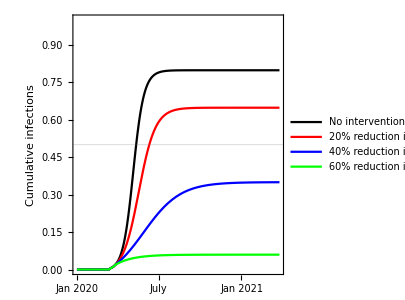

```mathematica
figoneshotinfnscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2xinfns],
Evaluate[1-Sq[t]/.sol40x2xinfns],
Evaluate[1-Sq[t]/.sol60x2xinfns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

## Plot break-pump strategy, no seasonality:

```mathematica
sf = 0.02;
```

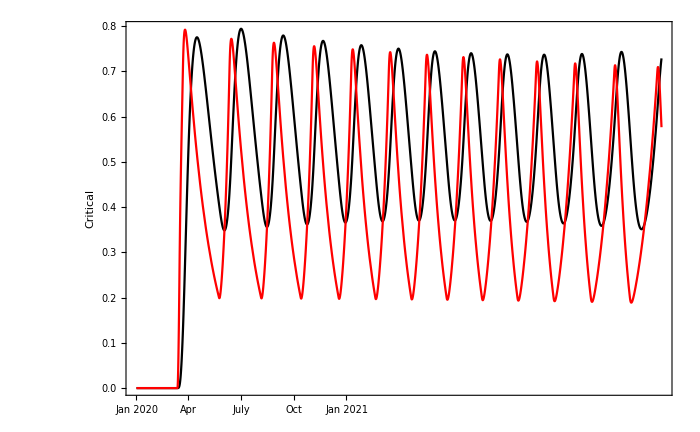

```mathematica
figcritprevbptemp = Plot[{
10000*Evaluate[CCq[t]/.sol60bpnsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpnsprev]
},Join[{t},plotwindowlong], PlotRange->All, FrameTicks->{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}},Automatic}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Critical"}, ImageSize->imsz, PlotStyle->{line1char, line2char, line3char, line4char},GridLines->{{},{}}]
```

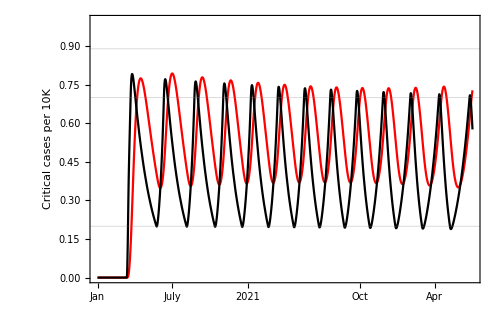

```mathematica
figcritprevbp = Plot[{
10000*Evaluate[CCq[t]/.sol60bpnsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpnsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,{#, ToString[(1/sf)*#]}&/@FindDivisions[PlotRange[figcritprevbptemp]⟦2⟧,5]},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Critical cases per 10K",None, "Prevalence per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

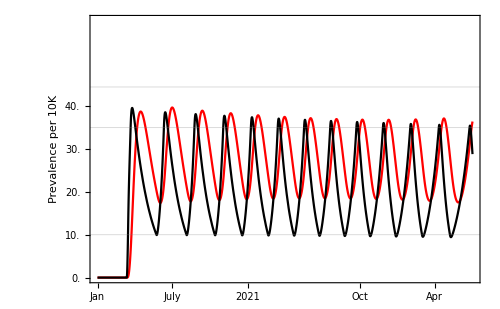

```mathematica
figcritprevbp = Plot[{
10000*Evaluate[CCq[t]/.sol60bpnsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpnsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1.2}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[PlotRange[figcritprevbptemp]⟦2⟧,5],All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibp = Plot[10*Evaluate[1-npi[t]/.sol60bpnsprev],{t,0,130}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

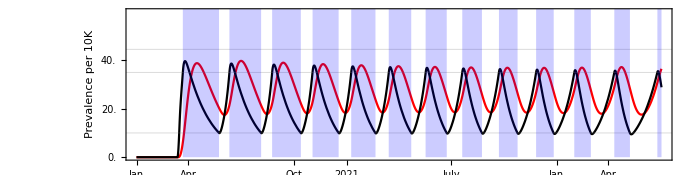

```mathematica
figcritprevbpnpi = Show[{figcritprevbp, fignpibp}, PlotRange->PlotRange[figcritprevbp], AspectRatio->ar, ImageSize->imsz]
```

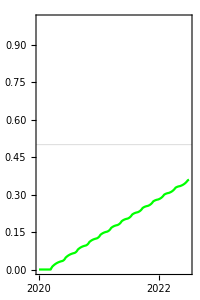

```mathematica
figcritprevbpnpiimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpnsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"},PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}, ImageSize-> 200]
```

## Plot break-pump strategy, with seasonality:

```mathematica
sf = 0.02;
```

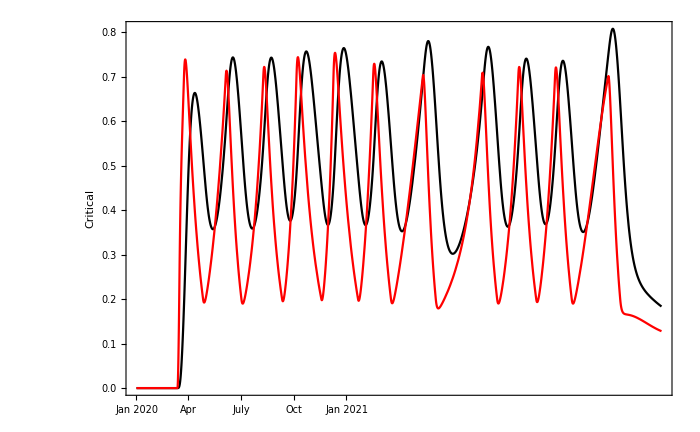

```mathematica
figcritprevbpstemp = Plot[{
10000*Evaluate[CCq[t]/.sol60bpsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpsprev]
},Join[{t},plotwindowlong], PlotRange->All, FrameTicks->{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}},Automatic}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Critical"}, ImageSize->imsz, PlotStyle->{line1char, line2char, line3char, line4char},GridLines->{{},{}}]
```

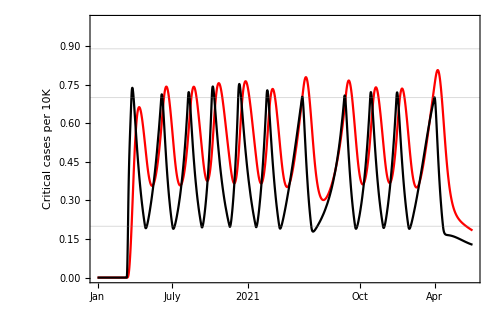

```mathematica
figcritprevbps = Plot[{
10000*Evaluate[CCq[t]/.sol60bpsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,{#, ToString[(1/sf)*#]}&/@FindDivisions[PlotRange[figcritprevbpstemp]⟦2⟧,5]},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Critical cases per 10K",None, "Prevalence per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

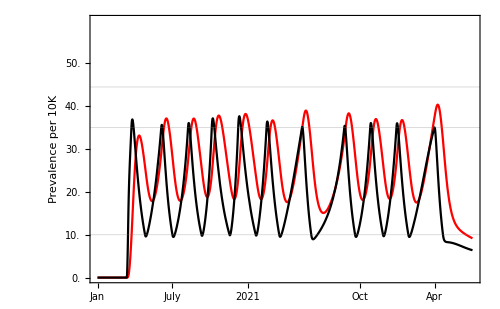

```mathematica
figcritprevbps = Plot[{
10000*Evaluate[CCq[t]/.sol60bpsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1.2}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[PlotRange[figcritprevbpstemp]⟦2⟧,5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibps = Plot[10*Evaluate[1-npi[t]/.sol60bpsprev],{t,0,130}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

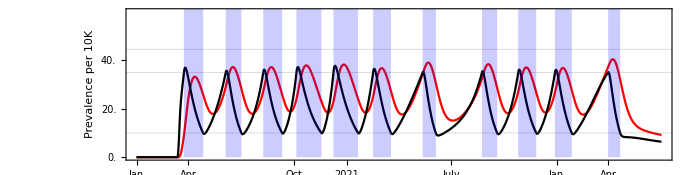

```mathematica
figcritprevbpsnpi = Show[{figcritprevbps, fignpibps}, PlotRange->PlotRange[figcritprevbps], AspectRatio->ar, ImageSize->imsz]
```

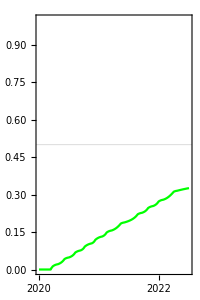

```mathematica
figcritprevbpsnpiimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

## Plot break-pump strategy, with seasonality, and double the ICU capacity:

```mathematica
sf = 0.02;
```

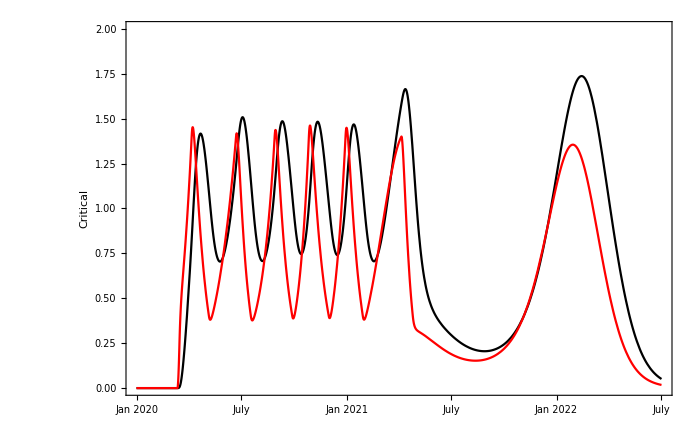

```mathematica
figcritprevbpsmoreICUtemp = Plot[{
10000*Evaluate[CCq[t]/.sol60bpsprevmoreICU],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0,2}, FrameTicks->{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"},
{52+(31+28+31)/7, "Apr"}, 
{52+(31+28+31+30+31+30)/7, "July"}, 
{52+(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52*2, "Jan\n2022"}, 
{52*2+(31+28+31)/7, "Apr"}, 
{52*2+(31+28+31+30+31+30)/7, "July"}, 
{52*2+(31+28+31+30+31+30+31+31+30)/7, "Oct"}},Automatic}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Critical"}, ImageSize->imsz, PlotStyle->{line1char, line2char, line3char, line4char},GridLines->{{},{}}]
```

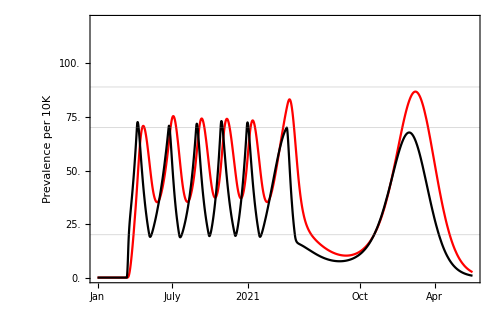

```mathematica
figcritprevbpsmoreICU = Plot[{
10000*Evaluate[CCq[t]/.sol60bpsprevmoreICU],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0, 2.4}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[PlotRange[figcritprevbpsmoreICUtemp]⟦2⟧,5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089*2,{Black, Opacity[1]}},  {10000*sf*thresholdprevonmoreICU, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoffmoreICU, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibpsmoreICU = Plot[10*Evaluate[1-npi[t]/.sol60bpsprevmoreICU],{t,0,100}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

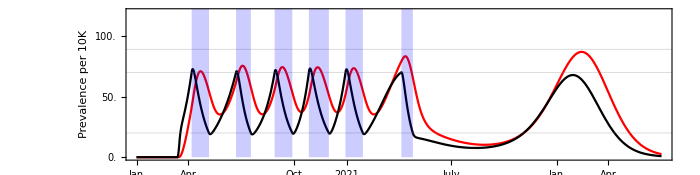

```mathematica
figcritprevbpsnpimoreICU = Show[{figcritprevbpsmoreICU, fignpibpsmoreICU}, PlotRange->PlotRange[figcritprevbpsmoreICU], AspectRatio->ar, ImageSize->imsz]
```

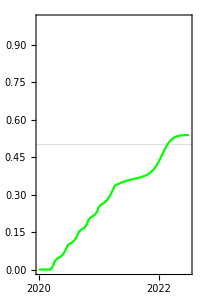

```mathematica
figcritprevbpsnpimoreICUimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

## Plot break-pump strategy, without seasonality, and double the ICU capacity:

```mathematica
sf = 0.02;
```

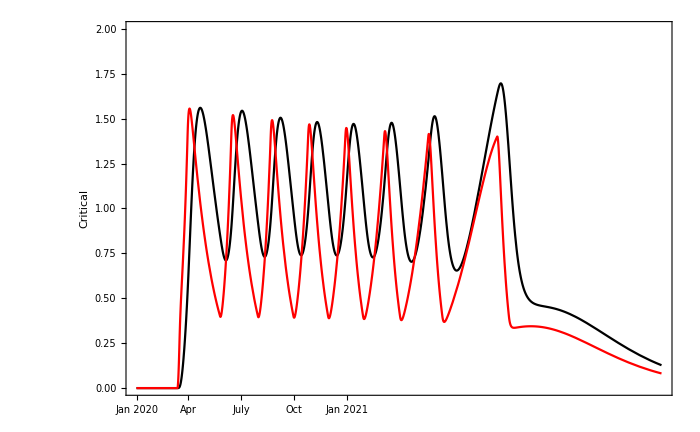

```mathematica
figcritprevbpnsmoreICUtemp = Plot[{
10000*Evaluate[CCq[t]/.sol60bpnsprevmoreICU],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpnsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0,2}, FrameTicks->{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}},Automatic}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Critical"}, ImageSize->imsz, PlotStyle->{line1char, line2char, line3char, line4char},GridLines->{{},{}}]
```

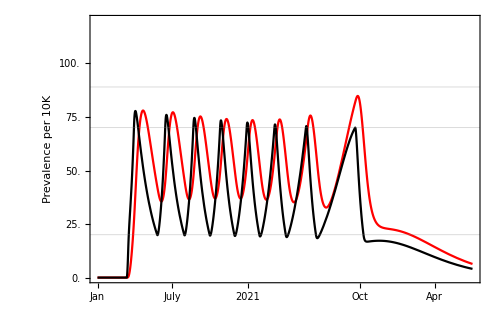

```mathematica
figcritprevbpnsmoreICU = Plot[{
10000*Evaluate[CCq[t]/.sol60bpnsprevmoreICU],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpnsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0, 2.4}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[PlotRange[figcritprevbpnsmoreICUtemp]⟦2⟧,5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089*2,{Black, Opacity[1]}},  {10000*sf*thresholdprevonmoreICU, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoffmoreICU, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibpnsmoreICU = Plot[10*Evaluate[1-npi[t]/.sol60bpnsprevmoreICU],{t,0,100}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

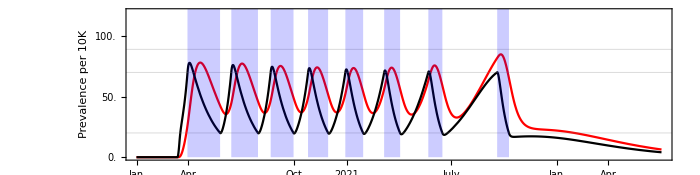

```mathematica
figcritprevbpnsnpimoreICU = Show[{figcritprevbpnsmoreICU, fignpibpnsmoreICU}, PlotRange->PlotRange[figcritprevbpnsmoreICU], AspectRatio->ar, ImageSize->imsz]
```

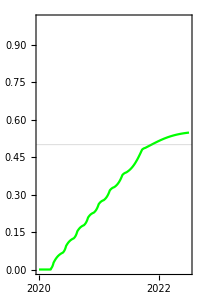

```mathematica
figcritprevbpnsnpimoreICUimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpnsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{ },{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```